```mathematica
S[x_]=4/Sqrt[10 Pi]Exp[-x^2/10];
Subscript[k, w][x_,ξ_]=Piecewise[{{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](x-ξ)],x<ξ}}];
Subscript[k, l][x_,ξ_]=Piecewise[{{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](x-ξ)],x<ξ}}];
var=Rationalize[{Subscript[α, w]->50.58,Subscript[β, w]->3.85/0.38,Subscript[η, w]->1/(0.38*10)*Q,Subscript[α, l]->192.2/(1.89*10),Subscript[β, l]->3.85/1.89,Subscript[η, l]->1/(1.89*10)*Q,Subscript[a, 0]->0.6,Subscript[a, 1]->0.38,M->0.38/1.89,Subscript[L, 0]->-1,Subscript[L, 1]->1}];
```

```mathematica
Subscript[T, 0][ξ_]:=Limit[Subscript[c, 0] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ<Subscript[A, 0]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,-∞,Subscript[A, 0]},Assumptions->ξ<Subscript[A, 0]]+
Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,-∞,Subscript[A, 0]},Assumptions->ξ<Subscript[A, 0]]
Subscript[F, 0][ξ_]=Refine[Subscript[T, 0][ξ]/.var,ξ<Subscript[A, 0]<0];
```

```mathematica
Subscript[T, 1][ξ_]:=Limit[ Subscript[c, 1] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 1],Assumptions->ξ<Subscript[A, 1]]-
		Limit[ Subscript[c, 0] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ>Subscript[A, 0]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[A, 0],Subscript[A, 1]},Assumptions->{Subscript[A, 0]<ξ<Subscript[A, 1]}]+
Subscript[η, w](1-Subscript[a, 1])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[A, 0],Subscript[A, 1]},Assumptions->{Subscript[A, 0]<ξ<Subscript[A, 1]}]
Subscript[F, 1][ξ_]=Refine[Subscript[T, 1][ξ]/.var,{Subscript[A, 0]<0,Subscript[A, 1]>0,Subscript[A, 0]<ξ<Subscript[A, 1]}];
```

```mathematica
Subscript[T, 2][ξ_]:=-Limit[Subscript[c, 1] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 1],Assumptions->ξ>Subscript[A, 1]]-
Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[A, 1],∞},Assumptions->ξ>Subscript[A, 1]]+
Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[A, 1],∞},Assumptions->ξ>Subscript[A, 1]]
Subscript[F, 2][ξ_]=Refine[Subscript[T, 2][ξ]/.var,ξ>Subscript[A, 1]>0];
```

```mathematica
Subscript[eqn, 0]=Subscript[F, 0][Subscript[A, 0]]+1==0;
Subscript[eqn, 1]=Subscript[F, 1][Subscript[A, 0]]+1==0;
Subscript[eqn, 2]=Subscript[F, 1][Subscript[A, 1]]+1==0;
Subscript[eqn, 3]=Subscript[F, 2][Subscript[A, 1]]+1==0;
```

```mathematica
Subscript[Q, min]=440;
Subscript[Q, max]=600;
(*n=2(Subscript[Q, max]-Subscript[Q, min])+1;*)
n=1
sols={};
Monitor[
For[i=0,i<n,i++,
(*tempQ={Q->Rationalize[Subscript[Q, min]+(Subscript[Q, max]-Subscript[Q, min])*i/(n-1),0]};*)
tempQ={SetPrecision[Q->441.5072,30]};
sol=Quiet[FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3]}/.tempQ,{{Subscript[c, 0],0},{Subscript[c, 1],0},{Subscript[A, 0],-1},{Subscript[A, 1],1}},MaxIterations->100,WorkingPrecision->30]];
sol=Join[sol,tempQ];
conds=Quiet[Subscript[A, 0]<Subscript[A, 1]&&
Abs[Subscript[F, 0][Subscript[A, 0]]+1]<0.000001&&
Abs[Subscript[F, 2][Subscript[A, 1]]+1]<0.000001/.sol];
If[conds,M[x_]=Piecewise[{{Subscript[F, 0][x],x<Subscript[A, 0]},{Subscript[F, 1][x],Subscript[A, 0]≤x≤Subscript[A, 1]},{Subscript[F, 2][x],Subscript[A, 1]<x}}/.sol];NUM=12001;points=SetPrecision[Table[-6+12(i-1)/(NUM-1),{i,NUM}],20];
nSolution=N[Map[M, points]];sols=Join[sols,{{N[Q/.sol],N[Subscript[F, 1][0]/.sol],nSolution}}],Nothing];
],{N[i/n],N[Q/.tempQ]}]
Beep[]
```

1

```mathematica
Export["C:\\masterA GitHub\\Code\\Gaussian\\Water\\2 - IceWaterIce_7.csv",sols,Format->Table];
```

{c_0→2.96141242494862777917000636026,c_1→-2.96141242494862777916224277239,A_0→-0.455577801087625714892998284623,A_1→0.455577801087625714887691611904}

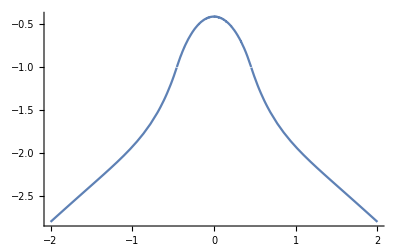

```mathematica
tempQ={SetPrecision[Q->441.507195,30]};
sol=FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3]}/.tempQ,{{Subscript[c, 0],0},{Subscript[c, 1],0},{Subscript[A, 0],-1},{Subscript[A, 1],1}},MaxIterations->100,WorkingPrecision->30]
sol=Join[tempQ,sol];
M[x_]=Piecewise[{{Subscript[F, 2][-x],x<Subscript[A, 0]},{Subscript[F, 1][x],Subscript[A, 0]≤x≤Subscript[A, 1]},{Subscript[F, 2][x],Subscript[A, 1]<x}}/.sol];
Plot[M[x],{x,-2,2}]
(*points=SetPrecision[Table[-6+12(i-1)/(5000-1),{i,5000}],30];*)
(*ListPlot[Map[M,points]]*)
```